```mathematica
Clear[a];Clear[f]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
a[.2,0.]=Import["/Users/jonahs/Desktop/camb/om2ol0.txt","table"];a[.2,.2]=Import["/Users/jonahs/Desktop/camb/om2ol2.txt","table"];a[.2,.4]=Import["/Users/jonahs/Desktop/camb/om2ol4.txt","table"];a[.2,.6]=Import["/Users/jonahs/Desktop/camb/om2ol6.txt","table"];a[.2,.8]=Import["/Users/jonahs/Desktop/camb/om2ol8.txt","table"];a[.2,1.]=Import["/Users/jonahs/Desktop/camb/om2ol10.txt","table"];a[.4,0.]=Import["/Users/jonahs/Desktop/camb/om4ol0.txt","table"];a[.4,.2]=Import["/Users/jonahs/Desktop/camb/om4ol2.txt","table"];a[.4,.4]=Import["/Users/jonahs/Desktop/camb/om4ol4.txt","table"];a[.4,.6]=Import["/Users/jonahs/Desktop/camb/om4ol6.txt","table"];a[.4,.8]=Import["/Users/jonahs/Desktop/camb/om4ol8.txt","table"];a[.4,1.]=Import["/Users/jonahs/Desktop/camb/om4ol10.txt","table"];a[.6,.2]=Import["/Users/jonahs/Desktop/camb/om6ol2.txt","table"];a[.6,0.]=Import["/Users/jonahs/Desktop/camb/om6ol0.txt","table"];a[.6,.4]=Import["/Users/jonahs/Desktop/camb/om6ol4.txt","table"];a[.6,.6]=Import["/Users/jonahs/Desktop/camb/om6ol6.txt","table"];a[.6,.8]=Import["/Users/jonahs/Desktop/camb/om6ol8.txt","table"];a[.6,1.]=Import["/Users/jonahs/Desktop/camb/om6ol10.txt","table"];a[.8,.2]=Import["/Users/jonahs/Desktop/camb/om8ol2.txt","table"];a[.8,0.]=Import["/Users/jonahs/Desktop/camb/om8ol0.txt","table"];a[.8,.4]=Import["/Users/jonahs/Desktop/camb/om8ol4.txt","table"];a[.8,.6]=Import["/Users/jonahs/Desktop/camb/om8ol6.txt","table"];a[.8,.8]=Import["/Users/jonahs/Desktop/camb/om8ol8.txt","table"];a[.8,1.]=Import["/Users/jonahs/Desktop/camb/om8ol10.txt","table"];a[1.,.2]=Import["/Users/jonahs/Desktop/camb/om8ol2.txt","table"];a[1.,0.]=Import["/Users/jonahs/Desktop/camb/om8ol0.txt","table"];a[1.,.4]=Import["/Users/jonahs/Desktop/camb/om8ol4.txt","table"];a[1.,.6]=Import["/Users/jonahs/Desktop/camb/om8ol6.txt","table"];a[1.,.8]=Import["/Users/jonahs/Desktop/camb/om8ol8.txt","table"];a[1.,1.]=Import["/Users/jonahs/Desktop/camb/om8ol10.txt","table"];
```

```mathematica
wmap=Import["/Users/jonahs/Desktop/wmap_bin.txt","table"];
```

```mathematica
(* import all the files into a in the form a["omega matter","omega lambda"] to easily access the camb outputs*)
```

```mathematica
p[i_,j_,k_]:={a[j,k][[i-1]][[1]],j,k}
```

```mathematica
(* here p is the position function in the 3 dimensional space of L, omega matter, omega lambda. this is to make sure everything is positioned correctly. note the form "a[j,k][[i-1]][[1]]" this is calling the file a[j,k] and then opening the i-1 th row and the first column entry *)
```

```mathematica
p[321,.4,.6]
```

{321,0.4,0.6}

```mathematica
val[i_,j_,k_]:=a[j,k][[i-1]][[2]]
```

```mathematica
(* here the val function outputs the Subscript[cl, TT] values from the camb run with omega matter of j and omega lambda value of k for the given l value of i-1. note the [[2]] refers to the second column of the file *)
```

```mathematica
val[321,.4,.6]
```

3126.2

```mathematica
A=Table[{p[i,j,k],val[i,j,k]},{i,2,2200},{j,.2,1,.2},{k,0,1,.2}];
```

```mathematica
(* we now make a table of all the values each element is of the form {{L,omega matter,omega lambda},{Subscript[CL, TT]}} this is the accepted format for the interpolation and this is stored in a 3 dimentional list. *)
```

```mathematica
B=Flatten[A,2];
```

```mathematica
(* here we flatten A the reson we are flattening it twice is because we had a 3 dimentional list and we want it to be a simple 1 dimentional list so we flatten it using order 2 to reduce the dimention of our list*)
```

```mathematica
f=ListInterpolation[Table[a[j,k][[i-1]][[2]],{i,2,2200},{j,.2,1,.2},{k,0,1,.2}],{{0,2200},{0,1},{0,1}}]
```

InterpolatingFunction[{{0., 2200.}, {0., 1.}, {0., 1.}}, <>]

```mathematica
(* using the above knowledge we can simply input the neccesary table into the list interpolation so the formatting is less critical.  *)
```

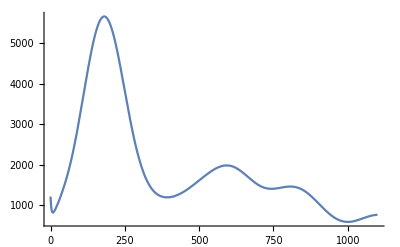

```mathematica
Plot[f[x,.3,.7],{x,0,1100}]
```

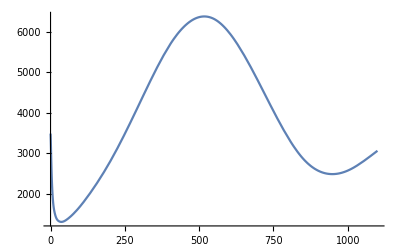
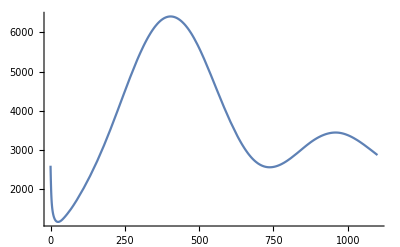
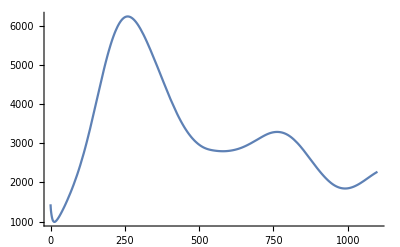
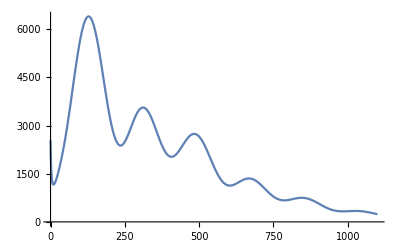
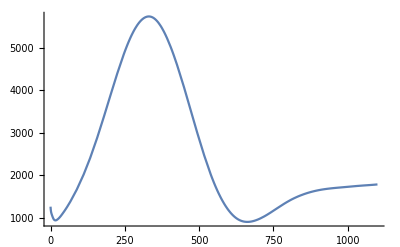
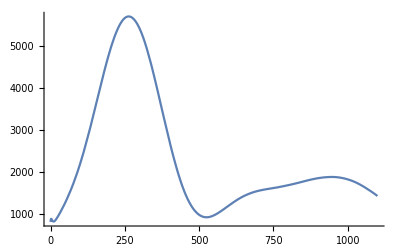
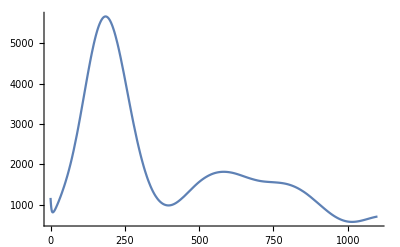
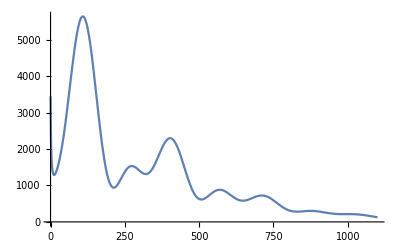

```mathematica
Table[Plot[f[x,i,j],{x,0,1100}],{i,0,1,1/3},{j,0,1,1/3}]
```

```mathematica
(* above is an easily manipulated function that plots power spectra for any inputed omega m and omega l *)
```

```mathematica
l[1]=46.6;l[2]=73.7;l[3]=107.2;l[4]=141.2;l[5]=175.8;l[6]=210.1;l[7]=244.2;l[8]=278.8;l[9]=313.1;tt[1]=878;tt[2]=1460;tt[3]=2920;tt[4]=5270;tt[5]=5450;tt[6]=6120;tt[7]=6310;tt[8]=4620;tt[9]=3610;er[1]=478;er[2]=400;er[3]=481;er[4]=552;er[5]=578;er[6]=586;er[7]=552;er[8]=468;er[9]=352;
```

```mathematica
(* this is the input of the BICEP2 data *)
```

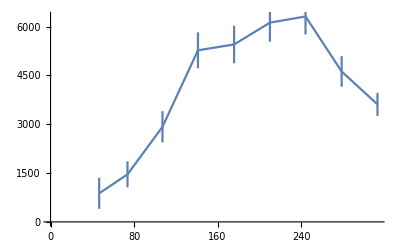

```mathematica
ErrorListPlot[{{{l[1],tt[1]},ErrorBar[er[1]]},{{l[2],tt[2]},ErrorBar[er[2]]},{{l[3],tt[3]},ErrorBar[er[3]]},{{l[4],tt[4]},ErrorBar[er[4]]},{{l[5],tt[5]},ErrorBar[er[5]]},{{l[6],tt[6]},ErrorBar[er[6]]},{{l[7],tt[7]},ErrorBar[er[7]]},{{l[8],tt[8]},ErrorBar[er[8]]},{{l[9],tt[9]},ErrorBar[er[9]]}},Joined->True]
```

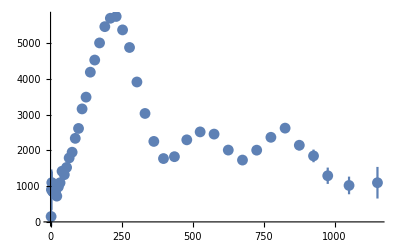

```mathematica
ErrorListPlot[Table[{{wmap[[i]][[1]],wmap[[i]][[4]]},ErrorBar[wmap[[i]][[5]]]},{i,1,45}]]
```

```mathematica
Clear[k2]
```

```mathematica
wl[i_]:=wmap[[i]][[1]];Do[wl[i],{i,1,45}];wtt[i_]:=wmap[[i]][[4]];Do[wtt[i],{i,1,45}];wer[i_]:=wmap[[i]][[5]];Do[wer[i],{i,1,45}];
```

```mathematica
(* here the wmap data is stored in a more convenient format for use in later functions*)
```

```mathematica
k2[Om_,Ol_]:=N[Sum[(wtt[i]-f[wl[i],Om,Ol])^2/wer[i]^2,{i,1,45}],4]
```

```mathematica
(* here a chi squared function is defined we skip the first few terms of the wmap data because they cause errors with certain values of Om and Ol *)
```

```mathematica
Plot3D[k2[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Clear[MC];Clear[Ol];Clear[Om];Ol[0]=.5;Om[0]=.5;
```

```mathematica
(* we make sure that all of our terms are clear before running the MCMC then give it starting parameters *)
```

```mathematica
s2[n_]:=ds2*RandomReal[{-1,1}];r2[n_]:=5000*RandomReal[{0,1}];ds2=.1;
```

```mathematica
(* here we define our acceptance ratios which should be the same order of dc *)
```

```mathematica
MC[n_]:=MC[n]=
(Ol1=RandomReal[{0,1}];
Om1=RandomReal[{0,1}];
(* the proposed steps are chosen randomly in the space 0 to 1. then the change in χ2 is calculated *)
dc[n]:=dc[n]=k2[Om1,Ol1]-k2[Om[n-1],Ol[n-1]];
If[dc[n]<0,
nkept[n]=1;Ol[n]:=Ol[n]=Ol1;Om[n]:=Om[n]=Om1,
(*if this step has a better χ2 then it is accepted *)
If[dc[n]<r2[n],nkept[n]=1;Ol[n]:=Ol[n]=Ol1;Om[n]:=Om[n]=Om1,
(* if the χ2 value is better than this random acceptance rate then we also accept the step *) 
nkept[n]=0;Ol[n]:=Ol[n]=Ol[n-1];Om[n]:=Om[n]=Om[n-1];]];
(* the step is rejected and we keep the old position *)
{Om[n],Ol[n]})
(* we print out our values at this step *)
```

```mathematica
chains=Table[MC[n],{n,0,10000}];
```

```mathematica
(*run the chain for 5000 steps *)
```

```mathematica
Mean[Flatten[Table[nkept[n],{n,1,10000}]]]//N
```

0.0844

```mathematica
(* test the acceptance ratio we want something around .2 - .4 *)
```

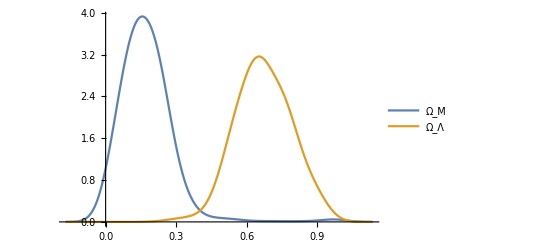

```mathematica
SmoothHistogram[{Table[MC[n][[1]],{n,3000,10000}],Table[MC[n][[2]],{n,3000,10000}]},.05,PlotLegends->{"Ω_M","Ω_Λ"}]
```

```mathematica
(* this is a histogram of the data *)
```

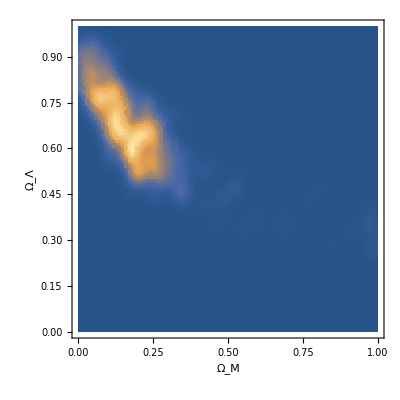

```mathematica
SmoothDensityHistogram[Table[MC[n],{n,3000,10000}],Automatic,Mesh->2,PlotRange->{{0,1},{0,1}},AxesLabel->{"Ω_M","Ω_Λ"}]
```

```mathematica
(* and the contour histogram of the liklihoods *)
```

```mathematica
(*z[1]=.863;z[2]=.538;z[3]=.778;z[4]=.355;z[5]=.497;z[6]=.638;z[7]=.43;z[8]=.644;z[9]=.74;z[10]=.543;mb[1]=24.95;mb[2]=23.02;mb[3]=24;mb[4]=22.02;mb[5]=22.96;mb[6]=23.85;mb[7]=22.75;mb[8]=23.26;mb[9]=23.75;mb[10]=23.27;e[1]=.44;e[2]=.17;e[3]=.42;e[4]=.15;e[5]=.2;e[6]=.33;e[7]=.18;e[8]=.27;e[9]=.37;e[10]=.14;*)
```

```mathematica
Z=Import["/Users/jonahs/Desktop/z.txt","list"];MB=Import["/Users/jonahs/Desktop/mb.txt","list"];
ER=Import["/Users/jonahs/Desktop/er.txt","list"];
```

```mathematica
Do[{z[i]=Z[[i]];mb[i]=MB[[i]];e[i]=ER[[i]]},{i,1,35}];
```

```mathematica
(*imported supernova data *)
```

```mathematica
mbmod[z_,Om_,Ol_,Mb_]:=25+5Log10[H0*Dl[z,Om,Ol]]-5Log10[H0]+Mb
```

```mathematica
(* model for the supernova data and input of given parameters *)
```

```mathematica
H0=2.3*10^-18;c=9.72*10^-15;q0[Om_,Ol_]:=.5Om-Ol;Dl[z_,Om_,Ol_]:=(c/H0)z (1-(z(1+(.5Om-Ol))/2)) ;Mb=-18.31300134478029;
```

```mathematica
χ2[Om_,Ol_,Mb_]:=N[Sum[(mb[i]-mbmod[z[i],Om,Ol,Mb])^2/e[i]^2,{i,1,35}]]
```

```mathematica
(* here is our chi squared value *)
```

```mathematica
s[n_]:=ds*RandomReal[{-1,1}];r[n_]:=20*RandomReal[{0,.5}];ds=.2;
```

```mathematica
(* similar to above we can control our acceptance ratios. and clear our parameters before runnning *)
```

```mathematica
Clear[MC3];Clear[ol];Clear[om];Clear[chains];Clear[nkept];ol[0]=.5;om[0]=.5;
```

```mathematica
MC3[n_]:=MC3[n]=
(ol1=RandomReal[{-1,3}];
om1=RandomReal[{0,3}];
(* the proposed steps are found and the change in χ2 is calculated *)
dc[n]:=dc[n]=Abs[χ2[om1,ol1,Mb]]-Abs[χ2[om[n-1],ol[n-1],Mb]];
If[dc[n]<0,
nkept[n]=1;ol[n]:=ol[n]=ol1;om[n]:=om[n]=om1,
(*if this step has a better χ2 then it is accepted *)
If[dc[n]<r[n],nkept[n]=1;ol[n]:=ol[n]=ol1;om[n]:=om[n]=om1,
(* if the χ2 value is better than this random shrinking acceptance rate then we also accept the step *) 
nkept[n]=0;ol[n]:=ol[n]=ol[n-1];om[n]:=om[n]=om[n-1];]];
(* the step is rejected and we keep the old position *)
{om[n],ol[n]})
(* we print out our values at this step *)
```

```mathematica
chains=Table[MC3[n],{n,0,10000}];
```

```mathematica
Mean[Flatten[Table[nkept[n],{n,1,10000}]]]//N
```

0.1074

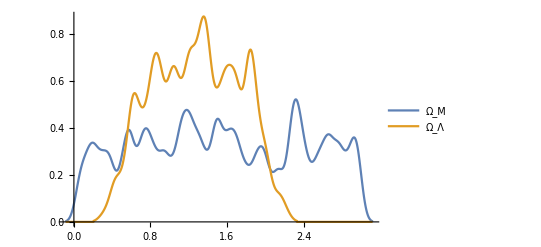

```mathematica
SmoothHistogram[{Table[MC3[n][[1]],{n,3000,10000}],Table[MC3[n][[2]],{n,3000,10000}]},.05,PlotLegends->{"Ω_M","Ω_Λ"}]
```

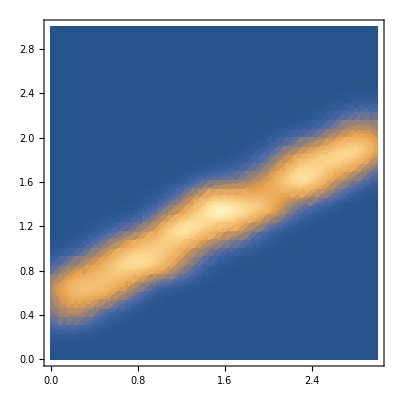

```mathematica
SmoothDensityHistogram[Table[MC3[n],{n,3000,10000}],Automatic,Mesh->2,PlotRange->{{0,3},{0,3}}]
```

```mathematica
t1=Table[MC3[n],{n,3000,10000}];t2=Table[MC[n],{n,3000,10000}];
```

```mathematica
t=Join[t1,t2];
```

```mathematica
(* here we combine our chains so that we have a joined chain that includes data from both runs overlaying the two contours *)
```

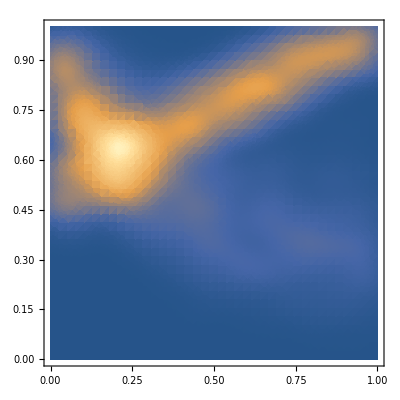

```mathematica
SmoothDensityHistogram[t,Automatic,Mesh->2,PlotRange->{{0,1},{0,1}}]
```

```mathematica
(* this is a plot of the two histograms simply overlayed to give a reference of how they look together *)
```

```mathematica
dist3=EstimatedDistribution[Table[MC3[n],{n,3000,10000}],BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ]]
```

BinormalDistribution[{1.53242,1.27818},{0.847353,0.444484},0.952999]

```mathematica
dist=EstimatedDistribution[Table[MC[n],{n,3000,10000}],BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ]]
```

BinormalDistribution[{0.173971,0.672537},{0.114392,0.1148},-0.760317]

```mathematica
(* these lines estimate the distribution functions for all the data in the form of binomial distributions *)
```

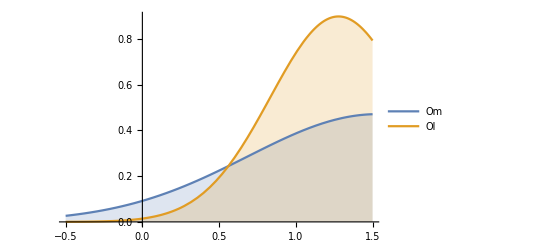

```mathematica
Plot[Evaluate[PDF[MarginalDistribution[dist3,#],x]&/@{1,2}],{x,-.5,1.5},Filling->Axis,PlotLegends->{"Om","Ol"}]
```

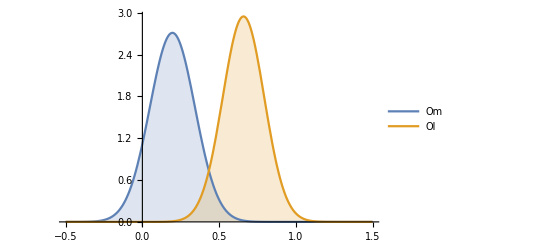

```mathematica
Plot[Evaluate[PDF[MarginalDistribution[dist,#],x]&/@{1,2}],{x,-.5,1.5},Filling->Axis,PlotLegends->{"Om","Ol"}]
```

```mathematica
(* here the distribution functions are plotted individually*)
```

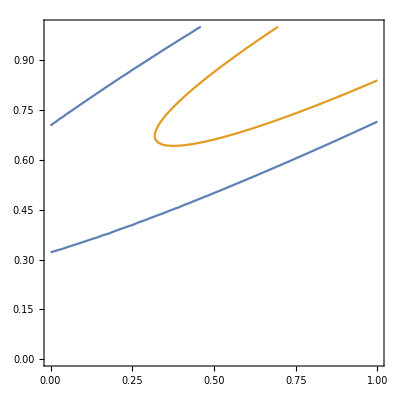

```mathematica
ContourPlot[{PDF[dist3,{x,y}]==.1,PDF[dist3,{x,y}]==.5},{x,0,1},{y,0,1},Contours->2,PlotRange->Full]
```

```mathematica
NIntegrate[Boole[PDF[dist3,{x,y}]≥ .1]*PDF[dist3,{x,y}],{x,-2,5},{y,-2,5}]
```

0.928302+1.85881×10^-31 ⅈ

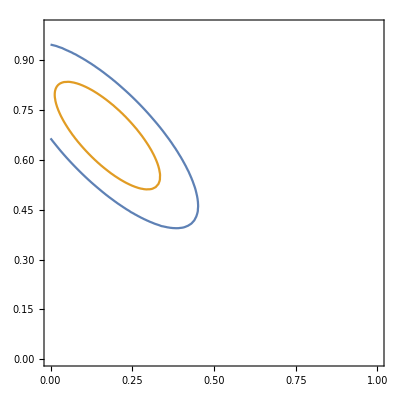

```mathematica
ContourPlot[{PDF[dist,{x,y}]/0.9876904067279219== 1,PDF[dist,{x,y}]/0.9876904067279219==7},{x,0,1},{y,0,1},Contours->2,PlotRange->Full]
```

```mathematica
NIntegrate[Evaluate[Boole[PDF[dist,{x,y}]/0.9876904067279219≥7]*PDF[dist,{x,y}]]/0.9876904067279219,{x,-1,1},{y,-1,1}]
```

0.637292+4.13839×10^-31 ⅈ

```mathematica
(* these are the joint contour plots of the two runs *)
```

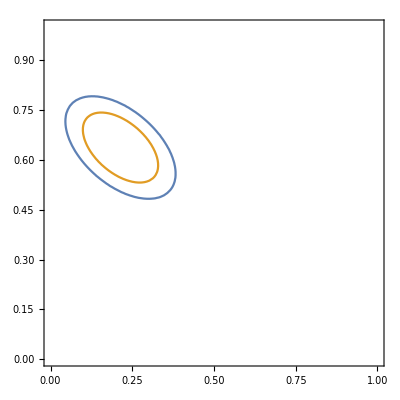

```mathematica
ContourPlot[{PDF[dist3,{x,y}]*PDF[dist,{x,y}]/0.22977602378951986==4,PDF[dist3,{x,y}]*PDF[dist,{x,y}]/0.22977602378951986==12},{x,0,1},{y,0,1},PlotRange->Full]
```

```mathematica
NIntegrate[Boole[PDF[dist3,{x,y}]*PDF[dist,{x,y}]/0.22977602378951986≥4]*PDF[dist3,{x,y}]*PDF[dist,{x,y}]/0.22977602378951986,{x,0,1},{y,0,1}]
```

0.932384+4.87909×10^-31 ⅈ

```mathematica
(* this is the combined countour plot of the two binomial distributions showing how percise it becomes when we combine the data *)
```

```mathematica
(*beyond this point is still being worked on and so hasn't been comented on *)
```

```mathematica
distt[x_,y_]:=PDF[dist3,{x,y}]*PDF[dist,{x,y}]
```

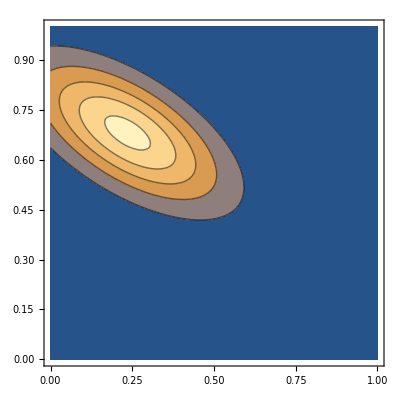

```mathematica
ContourPlot[distt[x,y],{x,0,1},{y,0,1},PlotRange->Full]
```